```mathematica
(*Legendre associated polynomial function*)
LGP[j_,m_,θ_]:=√((2 j+1)/(4π)((j-m)!)/((j+m)!))LegendreP[j,m,Cos[θ]]

(*Clebsh-Gordan function*)
CG[j_,m_,n_,J_,M_]:=If[m+n==M &&Abs[M]<=J && Abs[m]<= j && Abs[n] <= j,
ClebschGordan[{j,m},{j,n},{J,M}],
0
]


(*Ladder operators.Necessary the checks Abs[m]<=j,otherwise it returns an imaginary number*)
Cplus[j_,m_]:=If[Abs[m]<=j, √(j (j+1)-m (m+1))   ,0]
Cminus[j_,m_]:=If[Abs[m]<=j,√(j (j+1)-m (m-1))  ,0]
```

```mathematica
(*Integrals*)

(*φ integral when O=Subscript[Z, 1] Subscript[Z, 2]*)
IntZZ[m_, n_] := Module[{numerator,denominator, result},
If [m==n, result = 0,

(*otherwise, if m≠n*)
numerator = ⅈ (-1+ⅇ^(ⅈ (-m+n)π/2))^3 (1+ⅇ^(ⅈ (-m+n)π/2));
denominator = m-n;

result = numerator/denominator];

result // Chop
]

(*φ integral when O=Subscript[X, 1] Subscript[X, 2]*)
IntXX[m_,n_]:=Module[{numerator,denominator,result},
If[m==n,result=1/2 ⅇ^(-3/2 ⅈ m π) (1+ⅇ^(ⅈ m π)+ⅇ^(2 ⅈ m π)+ⅇ^(3 ⅈ m π)) π,

(*otherwise, if m≠n*)
result=-1/(m-n)ⅈ ⅇ^(-2 ⅈ m π) (ⅇ^((ⅈ m π)/2)-ⅇ^((ⅈ n π)/2)+ⅇ^(1/2 ⅈ (2 m+n) π)-ⅇ^(1/2 ⅈ (m+2 n) π)+ⅇ^(1/2 ⅈ (3 m+2 n) π)-ⅇ^(1/2 ⅈ (2 m+3 n) π)+ⅇ^(1/2 ⅈ (4 m+3 n) π)-ⅇ^(1/2 ⅈ (3 m+4 n) π));
];

result // Chop
]


ClearAll[Integral]

(*Define a cache to memorize the results of the integrals*)
integralCacheExact=<||>;

(*Function to calculate the integral with caching*)
Integral[j_,m_,n_]:=Module[{key,result},

(*Generate a unique key for  and *)
key=Sort[{m,n}];

(*If the integral is already calculated, it's recovered in the cache*)
If[KeyExistsQ[integralCacheExact,key],

result=integralCacheExact[key],

(*Otherwise it calculates the integral and it memorize in the cache*)
If[Abs[m]>j||Abs[n]>j,Return[0]];

integralPhi=IntXX[m,n];

If[integralPhi==0,
result=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];

result=Chop[integralPhi*integralTheta]
];

(*memorize in the cache*)
integralCacheExact[key]=result;];

result
]
```

```mathematica
TermList[j_,m_, n_, J_, M_]:=Module[{cgm1,cgm2,term1,term2,finalTerm,output,fileName},

cgm1=CG[j,m,M-m,J,M];
cgm2=CG[j,n,M-n,J,M];
term1=Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1];
term2=Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1];
finalTerm=cgm1*cgm2*term1*term2;

If[NumericQ[finalTerm],
Return[finalTerm];
];

]
```

0.0000115525

0.0000115525

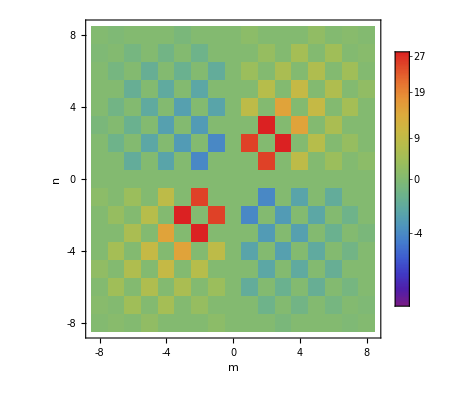

```mathematica
jj =8;
JJ = 2*jj-1;
MM =0;

Print[TermList[jj, jj-1, jj, JJ, MM]]
Print[TermList[jj, jj, jj-1, JJ, MM]]

ttt = Table[TermList[jj, mm, nn, JJ, MM], {mm, -jj, jj}, {nn, -jj, jj}];

MatrixPlot[ttt,
ColorFunction->"Rainbow",
PlotLegends->BarLegend["Rainbow"],
FrameTicks->{Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}]],Reverse[Table[{i,i-jj-1},{i,1,2*jj+1,4}] ]},
FrameLabel->{"n","m"},FrameTicksStyle->Directive[FontSize->12], DataReversed->{True, False}
]
```